# Hurricanes in the XXI century

David Torres
Nature Services Peru / University of California, Santa Cruz
June, 30, 2019

Weather forecasting has been significantly improved during the past century. On the other hand, climate prediction is still unclear and, therefore, we should take precautions and get ready for surprises. Our rapid urbanization signals that we are willing to take a lot of risk or that we are not paying enough attention. Let’s analyze the case of hurricanes in the XXI century from the data set “TropicalStorm” for the period 2000-2018.

First, we should do a list of their names using the functions "JoinString" and "ToString".

```mathematica
Hurricanes2000To2018=Table[EntityList[EntityClass["TropicalStorm","Hurricanes"<>ToString[year]]],{year,2000,2018}]//Short
```

{{Aletta,Carlotta,Daniel,Alberto,Gilma,Hector,Debby,Lane,Florence,Gordon,Isaac,Joyce,Keith,Michael},{Adolph,Dalila,Flossie,Erin,Gil,Felix,Gabrielle,Juliette,Kiko,Humberto,Iris,Karen,Narda,Michelle,Octave,Noel,Olga},«16»,{Alberto,Aletta,Beryl,Bud,Carlotta,Chris,Daniel,Debby,Emilia,Ernesto,Fabio,Florence,Gilma,Gordon,Hector,Helene,Ileana,Isaac,John,Joyce,Kirk,Kristy,Lane,Leslie,Michael,Miriam,Nadine,Norman,Olivia,Oscar,Paul,Rosa,Sergio,Tara,Vicente,Willa,Xavier}}

Second, let’s use their wind speed as a proxy of their magnitude. Using the functions “EntityProperty” and “Map” is one way to do it.

```mathematica
EntityProperty["TropicalStorm", "WindSpeed"]
```

wind speed

```mathematica
HurricanesSpeeds2000To2018=Map[#[EntityProperty["TropicalStorm","WindSpeed"]]&,Hurricanes2000To2018,{2}]
```

{{28.7695 mi/h,28.7695 mi/h,28.7695 mi/h,34.5234 mi/h,28.7695 mi/h,28.7695 mi/h,34.5234 mi/h,28.7695 mi/h,57.539 mi/h,34.5234 mi/h,51.7851 mi/h,28.7695 mi/h,23.0156 mi/h,69.0468 mi/h},{34.5234 mi/h,28.7695 mi/h,28.7695 mi/h,46.0312 mi/h,28.7695 mi/h,28.7695 mi/h,63.2929 mi/h,28.7695 mi/h,28.7695 mi/h,51.7851 mi/h,34.5234 mi/h,46.0312 mi/h,28.7695 mi/h,63.2929 mi/h,34.5234 mi/h,57.539 mi/h,34.5234 mi/h},{28.7695 mi/h,28.7695 mi/h,17.2617 mi/h,40.2773 mi/h,23.0156 mi/h,23.0156 mi/h,23.0156 mi/h,23.0156 mi/h,46.0312 mi/h,28.7695 mi/h,40.2773 mi/h,40.2773 mi/h},{28.7695 mi/h,23.0156 mi/h,28.7695 mi/h,23.0156 mi/h,46.0312 mi/h,28.7695 mi/h,28.7695 mi/h,23.0156 mi/h,23.0156 mi/h,51.7851 mi/h,57.539 mi/h,28.7695 mi/h,28.7695 mi/h,23.0156 mi/h},{57.539 mi/h,28.7695 mi/h,28.7695 mi/h,34.5234 mi/h,34.5234 mi/h,23.0156 mi/h,28.7695 mi/h,23.0156 mi/h,40.2773 mi/h,23.0156 mi/h,28.7695 mi/h,34.5234 mi/h,23.0156 mi/h,40.2773 mi/h,34.5234 mi/h,51.7851 mi/h},{23.0156 mi/h,23.0156 mi/h,11.5078 mi/h,28.7695 mi/h,57.539 mi/h,23.0156 mi/h,28.7695 mi/h,28.7695 mi/h,51.7851 mi/h,40.2773 mi/h,34.5234 mi/h,23.0156 mi/h,28.7695 mi/h,28.7695 mi/h,34.5234 mi/h,23.0156 mi/h,23.0156 mi/h,28.7695 mi/h,34.5234 mi/h,46.0312 mi/h,23.0156 mi/h,28.7695 mi/h},{23.0156 mi/h,28.7695 mi/h,28.7695 mi/h,28.7695 mi/h,34.5234 mi/h,23.0156 mi/h,23.0156 mi/h,28.7695 mi/h,23.0156 mi/h,57.539 mi/h,28.7695 mi/h,46.0312 mi/h,28.7695 mi/h,40.2773 mi/h,28.7695 mi/h,28.7695 mi/h},{28.7695 mi/h,28.7695 mi/h,28.7695 mi/h,34.5234 mi/h,34.5234 mi/h,17.2617 mi/h,23.0156 mi/h,17.2617 mi/h,34.5234 mi/h,23.0156 mi/h,51.7851 mi/h},{23.0156 mi/h,51.7851 mi/h,28.7695 mi/h,23.0156 mi/h,23.0156 mi/h,23.0156 mi/h,23.0156 mi/h,23.0156 mi/h,40.2773 mi/h,40.2773 mi/h,28.7695 mi/h,46.0312 mi/h,23.0156 mi/h,34.5234 mi/h,28.7695 mi/h,23.0156 mi/h},{28.7695 mi/h,28.7695 mi/h,28.7695 mi/h,34.5234 mi/h,46.0312 mi/h,17.2617 mi/h,23.0156 mi/h,28.7695 mi/h,34.5234 mi/h,34.5234 mi/h,28.7695 mi/h},{23.0156 mi/h,23.0156 mi/h,34.5234 mi/h,34.5234 mi/h,28.7695 mi/h,40.2773 mi/h,69.0468 mi/h,34.5234 mi/h,28.7695 mi/h,28.7695 mi/h,23.0156 mi/h,23.0156 mi/h,23.0156 mi/h,63.2929 mi/h,40.2773 mi/h},{23.0156 mi/h,28.7695 mi/h,17.2617 mi/h,23.0156 mi/h,28.7695 mi/h,23.0156 mi/h,46.0312 mi/h,69.0468 mi/h,69.0468 mi/h,28.7695 mi/h,46.0312 mi/h,23.0156 mi/h,51.7851 mi/h,17.2617 mi/h,34.5234 mi/h,23.0156 mi/h,23.0156 mi/h},{28.7695 mi/h,23.0156 mi/h,23.0156 mi/h,28.7695 mi/h,28.7695 mi/h,23.0156 mi/h,34.5234 mi/h,23.0156 mi/h,34.5234 mi/h,23.0156 mi/h,17.2617 mi/h,63.2929 mi/h,51.7851 mi/h,34.5234 mi/h,46.0312 mi/h,28.7695 mi/h,23.0156 mi/h,28.7695 mi/h,34.5234 mi/h,34.5234 mi/h},{23.0156 mi/h,23.0156 mi/h,23.0156 mi/h,28.7695 mi/h,34.5234 mi/h,28.7695 mi/h,17.2617 mi/h,34.5234 mi/h,23.0156 mi/h,46.0312 mi/h,23.0156 mi/h},{34.5234 mi/h,17.2617 mi/h,28.7695 mi/h,28.7695 mi/h,23.0156 mi/h,40.2773 mi/h,23.0156 mi/h,23.0156 mi/h,23.0156 mi/h,28.7695 mi/h,28.7695 mi/h,40.2773 mi/h,23.0156 mi/h,28.7695 mi/h,28.7695 mi/h,23.0156 mi/h,23.0156 mi/h,23.0156 mi/h,57.539 mi/h,57.539 mi/h,57.539 mi/h,34.5234 mi/h},{28.7695 mi/h,28.7695 mi/h,23.0156 mi/h,23.0156 mi/h,23.0156 mi/h,23.0156 mi/h,51.7851 mi/h,34.5234 mi/h,63.2929 mi/h,34.5234 mi/h,28.7695 mi/h,17.2617 mi/h,34.5234 mi/h,17.2617 mi/h,28.7695 mi/h,28.7695 mi/h,28.7695 mi/h,51.7851 mi/h,23.0156 mi/h},{23.0156 mi/h,80.5546 mi/h,28.7695 mi/h,34.5234 mi/h,23.0156 mi/h,23.0156 mi/h,23.0156 mi/h,28.7695 mi/h,28.7695 mi/h,51.7851 mi/h,28.7695 mi/h,23.0156 mi/h,17.2617 mi/h,34.5234 mi/h,23.0156 mi/h,28.7695 mi/h,63.2929 mi/h,57.539 mi/h,17.2617 mi/h,34.5234 mi/h},{52. mi/h,35. mi/h,35. mi/h,29. mi/h,40. mi/h,29. mi/h,63. mi/h,17. mi/h,35. mi/h,46. mi/h,46. mi/h,35. mi/h,29. mi/h,40. mi/h,52. mi/h,35. mi/h,52. mi/h,46. mi/h,81. mi/h,23.0156 mi/h,34.5234 mi/h,34.5234 mi/h,51.7851 mi/h,34.5234 mi/h,28.7695 mi/h,40.2773 mi/h,17.2617 mi/h,34.5234 mi/h,23.0156 mi/h,34.5234 mi/h,28.7695 mi/h,40.2773 mi/h,28.7695 mi/h,17.2617 mi/h,28.7695 mi/h,17.2617 mi/h,17.2617 mi/h,17.2617 mi/h,23.0156 mi/h,34.5234 mi/h,17.2617 mi/h,51.7851 mi/h,34.5234 mi/h,34.5234 mi/h,28.7695 mi/h,28.7695 mi/h,23.0156 mi/h,46.0312 mi/h,23.0156 mi/h,34.5234 mi/h,28.7695 mi/h,40.2773 mi/h,46.0312 mi/h,34.5234 mi/h},{34.5234 mi/h,23.0156 mi/h,34.5234 mi/h,34.5234 mi/h,23.0156 mi/h,17.2617 mi/h,23.0156 mi/h,34.5234 mi/h,23.0156 mi/h,40.2773 mi/h,17.2617 mi/h,28.7695 mi/h,23.0156 mi/h,17.2617 mi/h,17.2617 mi/h,51.7851 mi/h,46.0312 mi/h,34.5234 mi/h,23.0156 mi/h,23.0156 mi/h,40.2773 mi/h,28.7695 mi/h,23.0156 mi/h,46.0312 mi/h,57.539 mi/h,34.5234 mi/h,34.5234 mi/h,46.0312 mi/h,28.7695 mi/h,46.0312 mi/h,23.0156 mi/h,34.5234 mi/h,34.5234 mi/h,34.5234 mi/h,28.7695 mi/h,23.0156 mi/h,23.0156 mi/h}}

Third, we can take a graphical look by organizing the data in a “BarChart”.

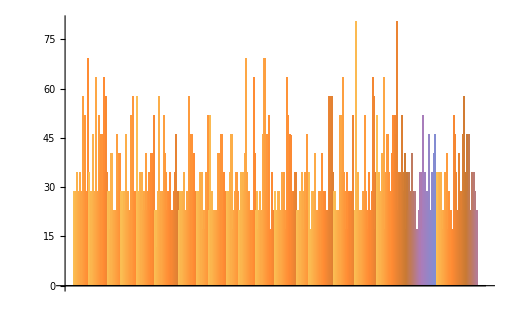

```mathematica
BarChart[HurricanesSpeeds2000To2018]
```

Fourth, we can also group the hurricanes per year with “Length” and have a more clear view with “BarChart”.

```mathematica
NumberOfHurricanes2000To2018=Length/@Hurricanes2000To2018
```

{14,17,12,14,16,22,16,11,16,11,15,17,20,11,22,19,20,54,37}

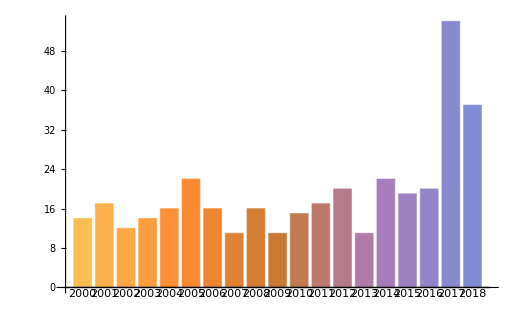

```mathematica
BarChart[{NumberOfHurricanes2000To2018},ChartLabels->{"2000","2001","2002","2003","2004","2005","2006","2007","2008","2009","2010","2011","2012","2013","2014","2015","2016","2017","2018"}]
```

Fifth,  we could see the higher values or stronger hurricanes for each year.

```mathematica
MaxHurricanesSpeeds2000To2018=Max@@@HurricanesSpeeds2000To2018
```

{69.0468 mi/h,63.2929 mi/h,46.0312 mi/h,57.539 mi/h,57.539 mi/h,57.539 mi/h,57.539 mi/h,51.7851 mi/h,51.7851 mi/h,46.0312 mi/h,69.0468 mi/h,69.0468 mi/h,63.2929 mi/h,46.0312 mi/h,57.539 mi/h,63.2929 mi/h,80.5546 mi/h,81. mi/h,57.539 mi/h}

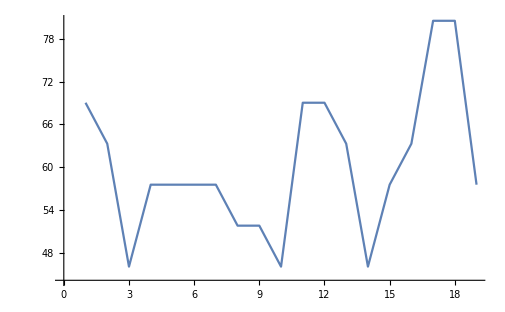

```mathematica
ListLinePlot[MaxHurricanesSpeeds2000To2018]
```

Finally, what this increase in the intensity of extreme events like hurricanes represents for society? that depends on the geographical distribution of the events and what is at risk in those areas. Fore example, in coastal zones, where most of the big cities are, the stakes are really high and getting bigger every year.

```mathematica
Interpreter["Image"][Import["/Users/davidtorres/Desktop/aaa5.png"]]
```

-Graphics-